# IPPT Model

## 5a. Backfill/Steady-State Comparison

Description:
- This notebook will import the results from “3b. Multiple-Pulse Data Export” for any propellant choice.
- Results are imported from WDX format from desired file path on PC. Auto-tethered to “Documents”.

How to Run:
- First, evaluate notebooks 1 and 2b for propellant of choice to get steady-state, multi-pulse data. Export data using 3b to create a WDX or CSV file type.
- Neutral backfill data is acquired from notebook 2c.
- Pull the desired file to “Documents” folder on PC, or to whichever folder Mathematica is auto-tethered.
- Either click “Evaluate Notebook” in Menu Options or import file manually.

## Data Import

Notes:
- Adjust the date the file was produced and the shot number to reflect desired data source

```mathematica
Filename1="2022-02-13_v1.12_run_21.wdx"; (* Filename1 set to backfill case *)
Filename2="2022-02-07_v1.12_run_9.wdx";(* Filename2+ set to multi-pulse import *)

shotdata1 = Import[Filename1];
shotdata2 = Import[Filename2];
```

## Unpack Data

```mathematica
(** Dataset 1 - Backfill **)
(* ICs *)
zmax1=shotdata1[[1]];
zsteps1=shotdata1[[2]];
tmax1=shotdata1[[3]];
tsteps1=shotdata1[[4]];
zs01=shotdata1[[5]];
ws01=shotdata1[[6]];
χi01=shotdata1[[7]];
zχi1=shotdata1[[8]];
nn01=shotdata1[[9]];
zn1=shotdata1[[10]];
Te01=shotdata1[[11]];
Ti01=shotdata1[[12]];
Lc1=shotdata1[[13]];
L01=shotdata1[[14]];
Rc1=shotdata1[[15]];
C01=shotdata1[[16]];
V01=shotdata1[[17]];
zc1=shotdata1[[18]];
zc01=shotdata1[[19]];
rout1=shotdata1[[20]];
rin1=shotdata1[[21]];
frep1 = shotdata1[[22]];
Np1 =shotdata1[[23]]; 
(* Single-pulse backfill output *)
(* State variables *)
nn1=shotdata1[[24]];
ws1=shotdata1[[25]];
zs1=shotdata1[[26]];
vs1=shotdata1[[27]];
vf1=shotdata1[[28]];
ns1=shotdata1[[29]];
nf1=shotdata1[[30]];
Ic1=shotdata1[[31]];
Ip1=shotdata1[[32]];
M1=shotdata1[[33]];
V1=shotdata1[[34]];
Te1=shotdata1[[35]];
Ti1=shotdata1[[36]];
ps1=shotdata1[[37]];
KEs1=shotdata1[[38]];
Ef1=shotdata1[[39]];
(* Performance metrics *)
mbit1=shotdata1[[40]];
ms1[t_]=shotdata1[[41]];
Epi1=shotdata1[[42]];
Eel1=shotdata1[[43]];
Eind1[t_]=shotdata1[[44]];
Ecap1[t_]=shotdata1[[45]];
Eke1[t_]=shotdata1[[46]];
EkePl1[t_]=shotdata1[[47]];
EkeEnt1[t_]=shotdata1[[48]];
Ete1[t_]=shotdata1[[49]];
Ibit1[t_]=shotdata1[[50]];
Isp1[t_]=shotdata1[[51]];
ηm1[t_]=shotdata1[[52]];
MassFrac1[t_]=shotdata1[[53]];
ηT1[t_]=shotdata1[[54]];
ηTrec1[t_]=shotdata1[[55]];
Πion1[t_]=shotdata1[[56]];
Πion21[t_]=shotdata1[[57]];
Πcex21[t_]=shotdata1[[58]];

(** Dataset 2 - Multi-Pulse **)
(* ICs *)
zmax2=shotdata2[[1]];
zsteps2=shotdata2[[2]];
tmax2=shotdata2[[3]];
tsteps2=shotdata2[[4]];
zs02=shotdata2[[5]];
ws02=shotdata2[[6]];
χi02=shotdata2[[7]];
zχi2=shotdata2[[8]];
nn02=shotdata2[[9]];
zn2=shotdata2[[10]];
Te02=shotdata2[[11]];
Ti02=shotdata2[[12]];
Lc2=shotdata2[[13]];
L02=shotdata2[[14]];
Rc2=shotdata2[[15]];
C02=shotdata2[[16]];
V02=shotdata2[[17]];
zc2=shotdata2[[18]];
zc02=shotdata2[[19]];
rout2=shotdata2[[20]];
rin2=shotdata2[[21]];
frep2 = shotdata2[[22]];
Np2 =shotdata2[[23]]; 
(* Per-pulse performance metrics and nondimesionalized parameters *)
Isptable=shotdata2[[24]];
nttable=shotdata2[[25]];
ntrectable=shotdata2[[26]];
nmtable=shotdata2[[27]];
piion1table=shotdata2[[28]];
piion2table=shotdata2[[29]];
picextable=shotdata2[[30]];
(* Pulse 1 state/performance *)
nni=shotdata2[[31]];
wsi=shotdata2[[32]];
zsi=shotdata2[[33]];
vsi=shotdata2[[34]];
vfi=shotdata2[[35]];
nsi=shotdata2[[36]];
nfi=shotdata2[[37]];
Ici=shotdata2[[38]];
Ipi=shotdata2[[39]];
Mi=shotdata2[[40]];
Vi=shotdata2[[41]];
Tei=shotdata2[[42]];
Tii=shotdata2[[43]];
psi=shotdata2[[44]];
KEsi=shotdata2[[45]];
Efi=shotdata2[[46]];
mbiti=shotdata2[[47]];
msi[t_]=shotdata2[[48]];
Epii=shotdata2[[49]];
Eeli=shotdata2[[50]];
Eindi[t_]=shotdata2[[51]];
Ecapi[t_]=shotdata2[[52]];
Ekei[t_]=shotdata2[[53]];
EkePli[t_]=shotdata2[[54]];
EkeEnti[t_]=shotdata2[[55]];
Etei[t_]=shotdata2[[56]];
Ibiti[t_]=shotdata2[[57]];
Ispi[t_]=shotdata2[[58]];
ηmi[t_]=shotdata2[[59]];
MassFraci[t_]=shotdata2[[60]];
ηTi[t_]=shotdata2[[61]];
ηTreci[t_]=shotdata2[[62]];
Πioni[t_]=shotdata2[[63]];
Πion2i[t_]=shotdata2[[64]];
Πcex2i[t_]=shotdata2[[65]];
(* Pulse n state/performance *)
nnf=shotdata2[[66]];
wsf=shotdata2[[67]];
zsf=shotdata2[[68]];
vsf=shotdata2[[69]];
vff=shotdata2[[70]];
nsf=shotdata2[[71]];
nff=shotdata2[[72]];
Icf=shotdata2[[73]];
Ipf=shotdata2[[74]];
Mf=shotdata2[[75]];
Vf=shotdata2[[76]];
Tef=shotdata2[[77]];
Tif=shotdata2[[78]];
psf=shotdata2[[79]];
KEsf=shotdata2[[80]];
Eff=shotdata2[[81]];
mbitf=shotdata2[[82]];
msf[t_]=shotdata2[[83]];
Epif=shotdata2[[84]];
Eelf=shotdata2[[85]];
Eindf[t_]=shotdata2[[86]];
Ecapf[t_]=shotdata2[[87]];
Ekef[t_]=shotdata2[[88]];
EkePlf[t_]=shotdata2[[89]];
EkeEntf[t_]=shotdata2[[90]];
Etef[t_]=shotdata2[[91]];
Ibitf[t_]=shotdata2[[92]];
Ispf[t_]=shotdata2[[93]];
ηmf[t_]=shotdata2[[94]];
MassFracf[t_]=shotdata2[[95]];
ηTf[t_]=shotdata2[[96]];
ηTrecf[t_]=shotdata2[[97]];
Πionf[t_]=shotdata2[[98]];
Πion2f[t_]=shotdata2[[99]];
Πcex2f[t_]=shotdata2[[100]];
```

## Post-Processing Calculations

```mathematica
(* LC Frequency *)
τLC1=N[2π(C01 Lc2)^(1/2)];
τLC2=N[2π(C02 Lc2)^(1/2)];

(* Energy Fraction *)
EnergyFrac1[t_]=(Eke1[t]+KEs1[t])/(Eel1+Epi1-Ecap1[t]);
EnergyFraci[t_]=(Ekei[t]+KEsi[t])/(Eeli+Epii-Ecapi[t]); (* initial *)
EnergyFracf[t_]=(Ekef[t]+KEsf[t])/(Eelf+Epif-Ecapf[t]); (* final *)

(* Coupling Coefficient *)
k1[t_] = M1[t]/Lc1;
ki[t_] = Mi[t]/Lc2;
kf[t_] = Mf[t]/Lc2;

(* Ohmic Heating *)
Eohmic1=Interpolation[Table[{tt,NIntegrate[Rc1 Ic1[dt]^2,{dt,0,tt}]},{tt,0,tmax1,tmax1/20}]];
Eohmici=Interpolation[Table[{tt,NIntegrate[Rc2 Ici[dt]^2,{dt,0,tt}]},{tt,0,tmax2,tmax2/20}]];
Eohmicf=Interpolation[Table[{tt,NIntegrate[Rc2 Icf[dt]^2,{dt,0,tt}]},{tt,0,tmax2,tmax2/20}]];

(* Argon Model *)
ec=1.6 10^-19;   
me=9.11 10^-31; 
kb=1.38 10^-23;  
g0=9.81; 
γ=5/3;  
μ0=4π 10^-7; 
ϵ0=8.85 10^-12;   
σcx= 5 10^-19; 
σen=4 10^-20;  
Sion[Te_]:= 2.34 10^-14 Te^0.59 Exp[-17.44/Te]; 
Λ[ne_,Te_]:=Piecewise[{{23-Log[(ne 10^-6)^(1/2)Te^(-3/2)],Te<7.389},{24-Log[(ne 10^-6)^(1/2)Te^-1],Te≥7.389}}]
νei[ne_,Te_]:=2.91 10^-12 ne Te^(-3/2)Λ[ne,Te]
νen[nn_,Te_]:=nn σen ((8 ec Te)/(π me))^(1/2)  
ηcl[ne_,nn_,Te_]:=(me (νei[ne,Te]+νen[nn,Te]))/(ne ec^2)
δsd[Lterm_,Cp_,ne_,nn_,Te_]:=((2(ηcl[ne,nn,Te])(Lterm Cp)^(1/2))/μ0)^(1/2)  

(* Slip Losses *)
SlipLoss1[t_]=nf1[t](vs1[t]-vf1[t])UnitStep[(vs1[t]-vf1[t])];
SlipLossi[t_]=nfi[t](vsi[t]-vfi[t])UnitStep[(vsi[t]-vfi[t])];
SlipLossf[t_]=nff[t](vsf[t]-vff[t])UnitStep[(vsf[t]-vff[t])];

(* Ionization Losses *)
IonLoss1[t_]=Sion[Te1[t]] ns1[t] nf1[t] ws1[t];
IonLossi[t_]=Sion[Tei[t]] nsi[t] nfi[t] wsi[t];
IonLossf[t_]=Sion[Tef[t]] nsf[t] nff[t] wsf[t];

(* Skin Depth *)
δs1[t_]=δsd[L01+Lc1-M1[t]^2/Lc1,C01,ns1[t],nn1[zs1[t],t]+nf1[t],Te1[t]];
δsi[t_]=δsd[L02+Lc2-Mi[t]^2/Lc2,C02,nsi[t],nni[zsi[t],t]+nfi[t],Tei[t]];
δsf[t_]=δsd[L02+Lc2-Mf[t]^2/Lc2,C02,nsf[t],nnf[zsf[t],t]+nff[t],Tef[t]];

(* Transparency Parameters *)
Θem1[t_]=Exp[-3ws1[t]/δs1[t]];
Θemi[t_]=Exp[-3wsi[t]/δsi[t]];
Θemf[t_]=Exp[-3wsf[t]/δsf[t]];

Θmion1[t_]=Exp[(-ns1[t]ws1[t]Sion[Te1[t]])/vs1[t]];
Θmioni[t_]=Exp[(-nsi[t]wsi[t]Sion[Tei[t]])/vs2[t]];
Θmionf[t_]=Exp[(-nsf[t]wsf[t]Sion[Tef[t]])/vsf[t]];

Θmcex1[t_]=Exp[-ns1[t] ws1[t]σcx];
Θmcexi[t_]=Exp[-nsi[t] wsi[t]σcx];
Θmcexf[t_]=Exp[-nsf[t] wsf[t]σcx];
```

## Backfill Results

```mathematica
(** Plot Styles **)
T1Plot[Fun_,Plotlabel_,Axislabel_,scale_]:=
Plot[Fun[Τ τLC1]scale,{Τ,0,1},
PlotStyle-> Black,
PlotRange->{{0,1},All},
Frame->True,
AspectRatio->1,
PlotLabel-> StringJoin["Time-Evolution of ",Plotlabel],
FrameLabel->{"t / Τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
AdjT1Plot[Fun_,Plotlabel_,Axislabel_,scale_]:=
Plot[Fun[Τ τLC1]scale,{Τ,0.02,1},
PlotStyle-> Black,
PlotRange->{{0,1},All},
Frame->True,
AspectRatio->1,
PlotLabel-> StringJoin["Time-Evolution of ",Plotlabel],
FrameLabel->{"t / Τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];

(** Print ICs **)
Print["Axial boundary of simulation = ",zmax1," m"];
Print["Number of axial gridpoints = ",zsteps1];
Print["Maximum time of simulation = ",tmax1," s"];
Print["Number of timesteps = ",tsteps1];
Print["Initial current sheet location = ",zs01," m"];
Print["Initial current sheet width = ",ws01," m"];
Print["Pre-ionization fraction = ",χi01];
Print["Pre-ionization length scale = ",zχi1," m"];
Print["Characteristic ambient neutral density = ",nn01*10^-20," x 10^20 m^-3"];
Print["Characteristic ambient neutral length scale = ",zn1," m"];
Print["Initial electron temperature = ",Te01," eV"];
Print["Initial ion temperature = ",Ti01," eV"];
Print["Coil inductance = ",Lc1*10^6," uH"];
Print["Stray inductance = ",L01*10^9," nH"];
Print["Coil resistance = ",Rc1," Ohms"];
Print["Capacitance = ",C01*10^6," μF"];
Print["Capacitor voltage = ",V01*10^-3," kV"];
Print["Coil mutual coupling distance = ",zc1*10^2," cm"];
Print["Location of the coil with respect to the neutral gas injection plane = ",zc01*10^3," mm"];
Print["Thruster outer radius = ",rout1," m"];
Print["Thruster inner radius = ",rin1," m"];
Print["Pulse repetition rate = ",frep1/10^3," kHz"];
Print["Number of pulses = ",Np1];

(** Plot State Variables **)
Print[T1Plot[ws1,"Sheet Width","w_s (m)",1]];
Print[T1Plot[zs1,"Sheet Position","z_s (m)",1]];
Print[T1Plot[vs1,"Sheet Velocity","v_s (km/s)",10^-3]];
Print[T1Plot[vf1,"Fast Neutral Velocity","v_f (km/s)",10^-3]];
Print[T1Plot[ns1,"Sheet Density","n_s (m^-3)",1]];
Print[T1Plot[nf1,"Fast Neutral Density","n_f (m^-3)",1]];
Print[T1Plot[Ic1,"Coil Current","I_c (kA)",10^-3]];
Print[T1Plot[Ip1,"Plasma Current","I_p (kA)",10^-3]];
Print[T1Plot[M1,"Mutual Inductance","M (nH)",10^9]];
Print[T1Plot[V1,"Circuit Voltage","V_c (kV)",10^-3]];
Print[T1Plot[Te1,"Electron Temperature","T_e (eV)",1]];
Print[T1Plot[Ti1,"Ion Temperature","T_i (eV)",1]];
Print[T1Plot[ps1,"Slipped Neutral Momentum","p_s (µN•s)",10^6]];
Print[T1Plot[KEs1,"Kinetic Energy in Slipped Neutrals","KE_s (J)",1]];
Print[T1Plot[Ef1,"Ionization Energy","E_f (J)",1]];

(** Plot Performance Metrics **)
Print[T1Plot[Isp1,"Specific Impulse","I_sp (s)",1]];
Print[AdjT1Plot[ηm1,"Mass Utilization Efficiency","η_m (%)",10^2]];
Print[T1Plot[ηT1,"Thrust Efficiency","η_T (%)",10^2]];
Print[T1Plot[ηTrec1,"Thrust Efficiency (Recapture)","η_T (%)",10^2]];
Print[T1Plot[EnergyFrac1,"Electrical Efficiency","η_e (%)",10^2]];
```

## Steady-State Results

```mathematica
(** Plot Styles **)
T2Plot[Fun_,Plotlabel_,Axislabel_,scale_]:=
Plot[Fun[Τ τLC2]scale,{Τ,0,1},
PlotStyle-> Black,
PlotRange->{{0,1},All},
Frame->True,
AspectRatio->1,
PlotLabel-> StringJoin["Time-Evolution of ",Plotlabel],
FrameLabel->{"t / Τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
AdjT2Plot[Fun_,Plotlabel_,Axislabel_,scale_]:=
Plot[Fun[Τ τLC2]scale,{Τ,0.02,1},
PlotStyle-> Black,
PlotRange->{{0,1},All},
Frame->True,
AspectRatio->1,
PlotLabel-> StringJoin["Time-Evolution of ",Plotlabel],
FrameLabel->{"t / Τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
PulsePlot[Table_,Plotlabel_,Axislabel_]:=
ListLinePlot[Table,
PlotRange->All,
Frame->True,
ImageSize->400,
PlotLabel->StringJoin[Plotlabel," per Pulse"],
FrameLabel->{"Pulse Number",Axislabel},
Axes->False,
LabelStyle->{16,Black},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle-> {FontFamily->"Times"}];
NDensity3DPlot[Fun_,zmax_,tmax_]:=
Plot3D[Fun[z,t/10^6] 10^-20,{z,0,zmax},{t,0,tmax 10^6},
PlotRange->All,
ImageSize->400,
PlotLabel-> "Neutral Density Distribution",
AxesLabel->{"Position, z (m)","Time, t (μs)","n_n (×10^20 m^-3)"},
LabelStyle->{16,Black,FontFamily->"Times"},
ViewProjection->"Orthographic",
ViewPoint->{1,1,1}];

(** Print ICs **)
Print["Axial boundary of simulation = ",zmax2," m"];
Print["Number of axial gridpoints = ",zsteps2];
Print["Maximum time of simulation = ",tmax2," s"];
Print["Number of timesteps = ",tsteps2];
Print["Initial current sheet location = ",zs02," m"];
Print["Initial current sheet width = ",ws02," m"];
Print["Pre-ionization fraction = ",χi02];
Print["Pre-ionization length scale = ",zχi2," m"];
Print["Characteristic ambient neutral density = ",nn02*10^-20," x 10^20 m^-3"];
Print["Characteristic ambient neutral length scale = ",zn2," m"];
Print["Initial electron temperature = ",Te02," eV"];
Print["Initial ion temperature = ",Ti02," eV"];
Print["Coil inductance = ",Lc2*10^6," uH"];
Print["Stray inductance = ",L02*10^9," nH"];
Print["Coil resistance = ",Rc2," Ohms"];
Print["Capacitance = ",C02*10^6," μF"];
Print["Capacitor voltage = ",V02*10^-3," kV"];
Print["Coil mutual coupling distance = ",zc2*10^2," cm"];
Print["Location of the coil with respect to the neutral gas injection plane = ",zc02*10^3," mm"];
Print["Thruster outer radius = ",rout2," m"];
Print["Thruster inner radius = ",rin2," m"];
Print["Pulse repetition rate = ",frep2/10^3," kHz"];
Print["Number of pulses = ",Np2];

(** Plot State Variables **)
(* Pulse 1 *)
Print[T2Plot[wsi,"Sheet Width (N_(p, 0))","w_s (m)",1]];
Print[T2Plot[zsi,"Sheet Position (N_(p, 0))","z_s (m)",1]];
Print[T2Plot[vsi,"Sheet Velocity (N_(p, 0))","v_s (km/s)",10^-3]];
Print[T2Plot[vfi,"Fast Neutral Velocity (N_(p, 0))","v_f (km/s)",10^-3]];
Print[T2Plot[nsi,"Sheet Density (N_(p, 0))","n_s (m^-3)",1]];
Print[T2Plot[nfi,"Fast Neutral Density (N_(p, 0))","n_f (m^-3)",1]];
Print[T2Plot[Ici,"Coil Current (N_(p, 0))","I_c (kA)",10^-3]];
Print[T2Plot[Ipi,"Plasma Current (N_(p, 0))","I_p (kA)",10^-3]];
Print[T2Plot[Mi,"Mutual Inductance (N_(p, 0))","M (nH)",10^9]];
Print[T2Plot[Vi,"Circuit Voltage (N_(p, 0))","V_c (kV)",10^-3]];
Print[T2Plot[Tei,"Electron Temperature (N_(p, 0))","T_e (eV)",1]];
Print[T2Plot[Tii,"Ion Temperature (N_(p, 0))","T_i (eV)",1]];
Print[T2Plot[psi,"Slipped Neutral Momentum (N_(p, 0))","p_s (µN•s)",10^6]];
Print[T2Plot[KEsi,"Kinetic Energy in Slipped Neutrals (N_(p, 0))","KE_s (J)",1]];
Print[T2Plot[Efi,"Ionization Energy (N_(p, 0))","E_f (J)",1]];
(* Pulse n *)
Print[T2Plot[wsf,"Sheet Width (N_(p, f))","w_s (m)",1]];
Print[T2Plot[zsf,"Sheet Position (N_(p, f))","z_s (m)",1]];
Print[T2Plot[vsf,"Sheet Velocity (N_(p, f))","v_s (km/s)",10^-3]];
Print[T2Plot[vff,"Fast Neutral Velocity (N_(p, f))","v_f (km/s)",10^-3]];
Print[T2Plot[nsf,"Sheet Density (N_(p, f))","n_s (m^-3)",1]];
Print[T2Plot[nff,"Fast Neutral Density (N_(p, f))","n_f (m^-3)",1]];
Print[T2Plot[Icf,"Coil Current (N_(p, f))","I_c (kA)",10^-3]];
Print[T2Plot[Ipf,"Plasma Current (N_(p, f))","I_p (kA)",10^-3]];
Print[T2Plot[Mf,"Mutual Inductance (N_(p, f))","M (nH)",10^9]];
Print[T2Plot[Vf,"Circuit Voltage (N_(p, f))","V_c (kV)",10^-3]];
Print[T2Plot[Tef,"Electron Temperature (N_(p, f))","T_e (eV)",1]];
Print[T2Plot[Tif,"Ion Temperature (N_(p, f))","T_i (eV)",1]];
Print[T2Plot[psf,"Slipped Neutral Momentum (N_(p, f))","p_s (µN•s)",10^6]];
Print[T2Plot[KEsf,"Kinetic Energy in Slipped Neutrals (N_(p, f))","KE_s (J)",1]];
Print[T2Plot[Eff,"Ionization Energy (N_(p, f))","E_f (J)",1]];

(** Plot Performance Metrics **)
(* Pulse 1 *)
Print[T2Plot[Ispi,"Specific Impulse (N_(p, 0))","I_sp (s)",1]];
Print[AdjT2Plot[ηmi,"Mass Utilization Efficiency (N_(p, 0))","η_m (%)",10^2]];
Print[T2Plot[ηTi,"Thrust Efficiency (N_(p, 0))","η_T (%)",10^2]];
Print[T2Plot[ηTreci,"Thrust Efficiency (Recapture, N_(p, 0))","η_T (%)",10^2]];
Print[T2Plot[EnergyFraci,"Electrical Efficiency (N_(p, 0))","η_e (%)",10^2]];
(* Pulse n *)
Print[T2Plot[Ispf,"Specific Impulse (N_(p, f))","I_sp (s)",1]];
Print[AdjT2Plot[ηmf,"Mass Utilization Efficiency (N_(p, f))","η_m (%)",10^2]];
Print[T2Plot[ηTf,"Thrust Efficiency (N_(p, f))","η_T (%)",10^2]];
Print[T2Plot[ηTrecf,"Thrust Efficiency (Recapture, N_(p, f))","η_T (%)",10^2]];
Print[T2Plot[EnergyFracf,"Electrical Efficiency (N_(p, f))","η_e (%)",10^2]];

(** Print/Plot Per-Pulse Data **)
Print["Isp (s) = ",Isptable];
Print["Without energy recovery: ηT = ",nttable];
Print["With energy recovery: ηT = ",ntrectable];
Print["ηm = ",nmtable];
Print["Πion (1) = ",piion1table];
Print["Πion (2) = ",piion2table];
Print["Πcex = ",picextable];
Print[PulsePlot[Isptable,"Specific Impulse","I_sp (s)"]];
Print[PulsePlot[ntrectable,"Thrust Efficiency (Recapture)","η_T"]];
Print[PulsePlot[nmtable,"Mass Utilization Efficiency","η_m"]];
```

## Comparison Study

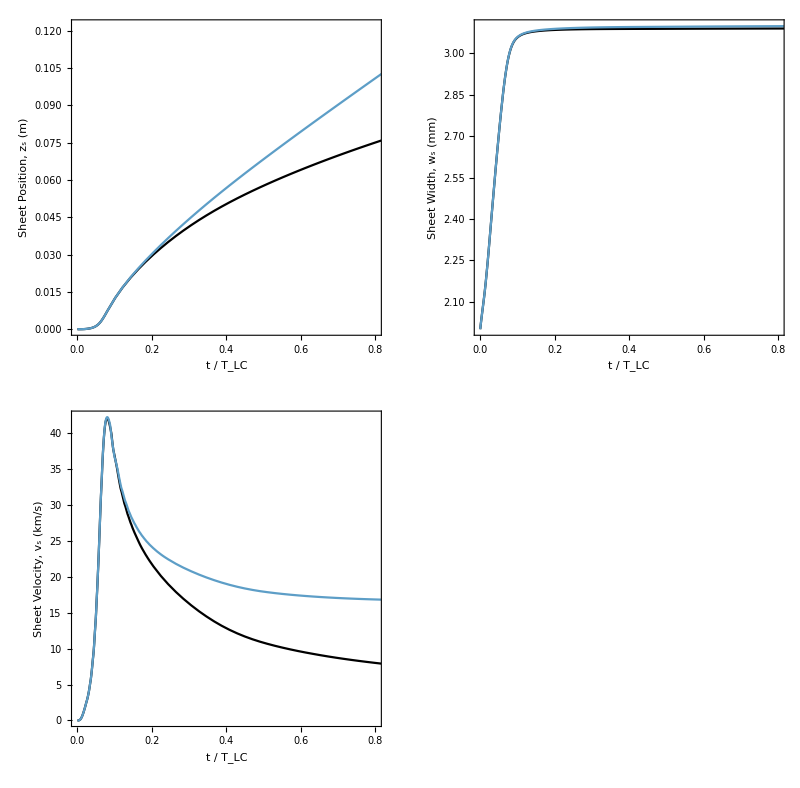

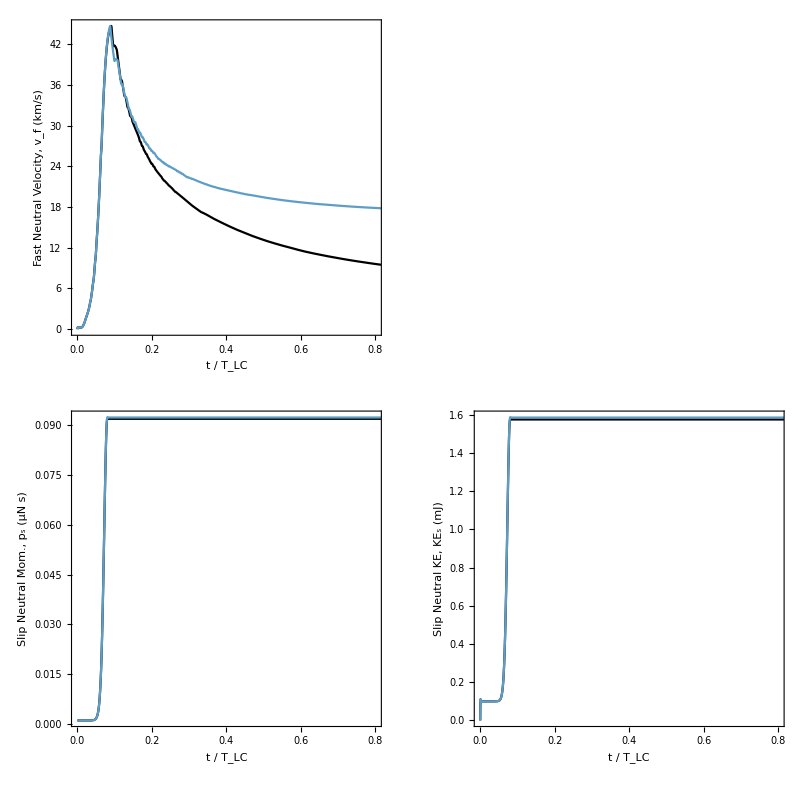

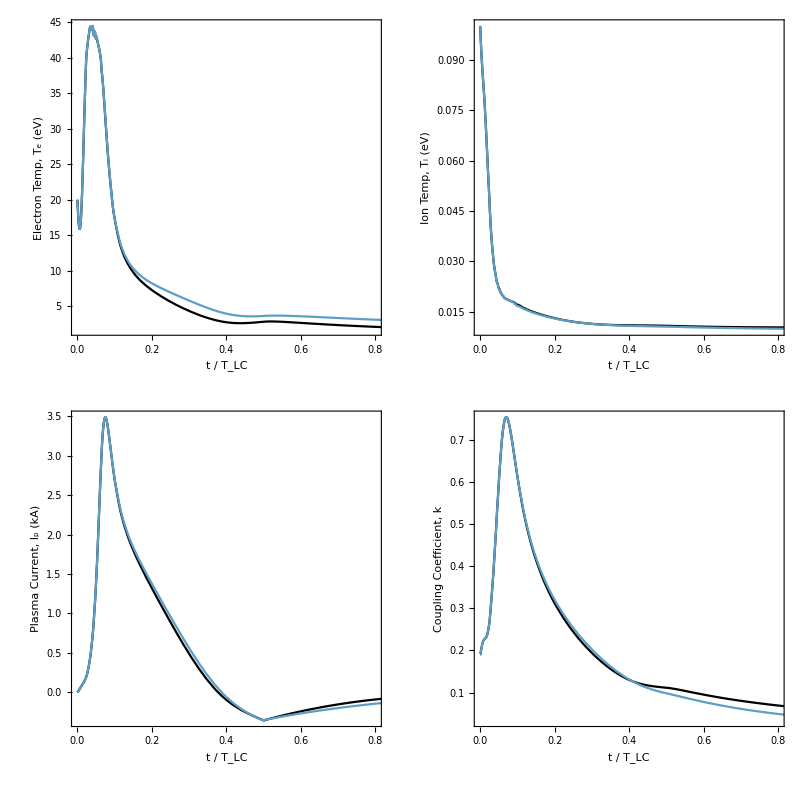

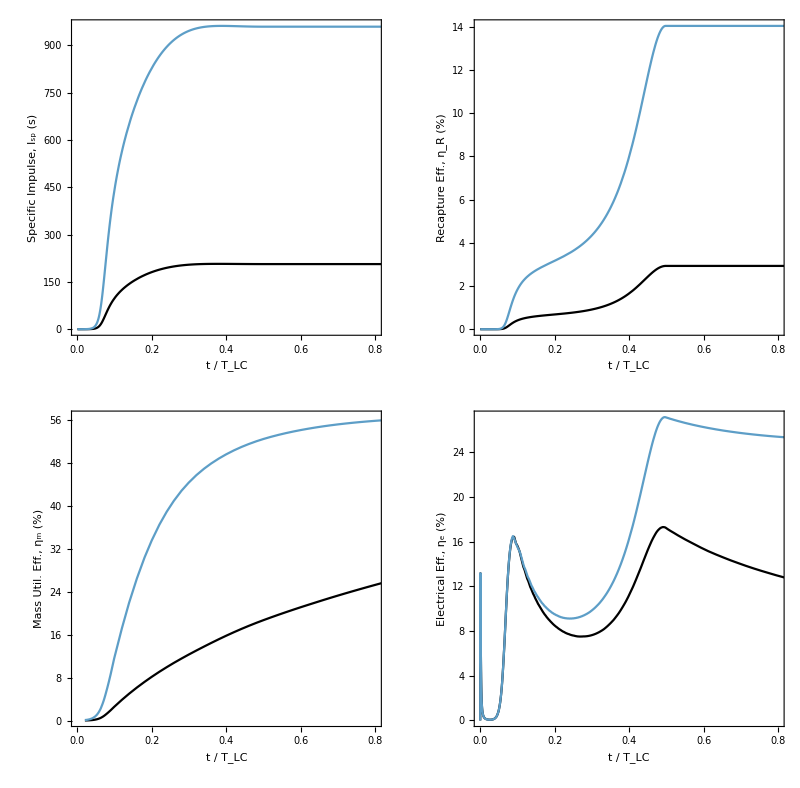

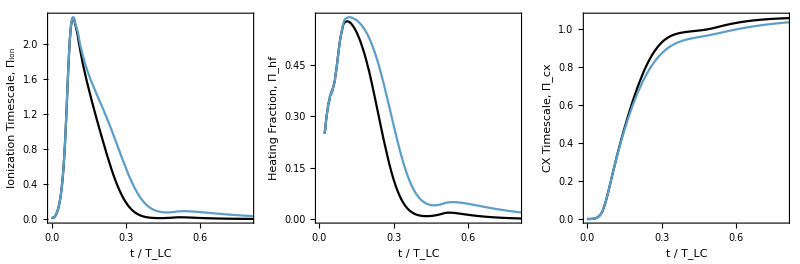

-Graphics-

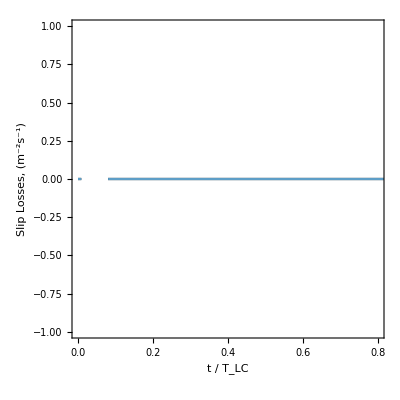

General::munfl: Exp[-1.14476×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.14468×10^6] is too small to represent as a normalized machine number; precision may be lost.

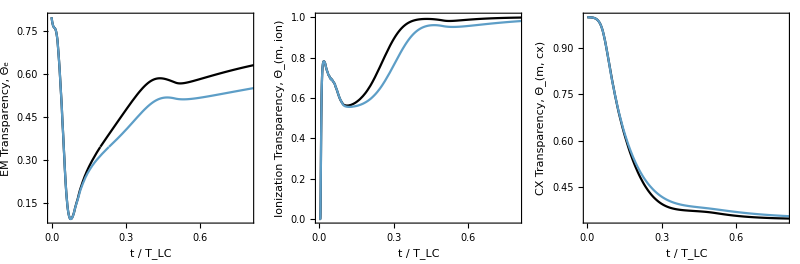

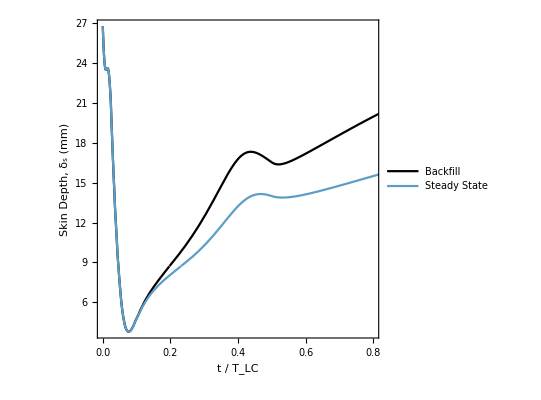

```mathematica
(** Plot Styles **)
Comp2Plot[Fun1_,Fun2_,Axislabel_,scale_]:=
Plot[{Fun1[Τ τLC1]scale,Fun2[Τ τLC2]scale},{Τ,0,1},
PlotRange->{{0,0.8},All},
PlotStyle->{Black,ColorData[97,"ColorList"][[7]]},
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
PlotLegends->{"Backfill","Steady State"},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
CompDevPlot[Fun1_,Fun2_,Axislabel_,scale_]:=
Plot[{Fun1[Τ τLC2]scale,Fun2[Τ τLC2]scale},{Τ,0,1},
PlotRange->{{0,0.8},All},
PlotStyle->{Black,ColorData[97,"ColorList"][[7]]},
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
PlotLegends->{"Transient","Steady-State"},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
GridPlot[Fun1_,Fun2_,Axislabel_,scale_]:=
Plot[{Fun1[Τ τLC1]scale,Fun2[Τ τLC2]scale},{Τ,0,1},
PlotRange->{{0,0.8},All},
PlotStyle->{Black,ColorData[97,"ColorList"][[7]]},
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
AdjGridPlot[Fun1_,Fun2_,Axislabel_,scale_]:=
Plot[{Fun1[Τ τLC1]scale,Fun2[Τ τLC2]scale},{Τ,0.02,1},
PlotRange->{{0,0.8},All},
PlotStyle->{Black,ColorData[97,"ColorList"][[7]]},
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
EModePlot[Fcap_,Fin_,Fun1_,Fun2_,Fun3_,Fun4_,Fun5_,Fun6_,Fun7_,τLC_,Plotlabel_]:=
Plot[{Fun1[Τ τLC]/(Fcap[Τ τLC]+Fin[Τ τLC]),Fun2[Τ τLC]/(Fcap[Τ τLC]+Fin[Τ τLC]),Fun3[Τ τLC]/(Fcap[Τ τLC]+Fin[Τ τLC]),Fun4[Τ τLC]/(Fcap[Τ τLC]+Fin[Τ τLC]),Fun5[Τ τLC]/(Fcap[Τ τLC]+Fin[Τ τLC]),Fun6[Τ τLC]/(Fcap[Τ τLC]+Fin[Τ τLC]),Fun7[Τ τLC]/(Fcap[Τ τLC]+Fin[Τ τLC])},{Τ,0,1},
PlotRange->{{0,0.8},{0,0.15}},
Frame->True,
ImageSize->400,
PlotLabel-> StringJoin[{"Energy Mode Comparison, ",Plotlabel}],
FrameLabel->{"t / Τ_LC","E / (E_cap+E_ind)"},
PlotLegends->{"total kinetic energy","kinetic energy in plasma","kinetic energy in entrained neutrals","kinetic energy in slipped neutrals","thermal energy","ionization energy","ohmic energy"},
PlotStyle->{{Thick,Black},{Dashed,Red},Green,Orange,Purple,Blue,Cyan},
Axes->False,
LabelStyle->{16,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]

(** Sheet Parameters **)
Print[GraphicsGrid[{
{GridPlot[zs1,zsf,"Sheet Position, z_s (m)",1],GridPlot[ws1,wsf,"Sheet Width, w_s (mm)",10^3]},
{GridPlot[vs1,vsf,"Sheet Velocity, v_s (km/s)",10^-3],GridPlot[ns1,nsf,"Plasma Density, n_s (m^-3)",1]}}
,Spacings-> {5,-5},ImageSize-> 800]];

(** Entrained/Slipped Neutrals **)
Print[GraphicsGrid[{
{GridPlot[vf1,vff,"Fast Neutral Velocity, v_f (km/s)",10^-3],GridPlot[nf1,nff,"Fast Neutral Density, n_f (m^-3)",1]},
{GridPlot[ps1,psf,"Slip Neutral Mom., p_s (μN s)",10^6],GridPlot[KEs1,KEsf,"Slip Neutral KE, KE_s (mJ)",10^3]}}
,Spacings-> {5,-5},ImageSize-> 800]];

(** Plasma **)
Print[GraphicsGrid[{
{GridPlot[Te1,Tef,"Electron Temp, T_e (eV)",1],GridPlot[Ti1,Tif,"Ion Temp, T_i (eV)",1]},
{GridPlot[Ip1,Ipf,"Plasma Current, I_p (kA)",10^-3],GridPlot[k1,kf,"Coupling Coefficient, k",1]}}
,Spacings-> {5,-5},ImageSize-> 800]];

(** Performance **)
Print[GraphicsGrid[{
{GridPlot[Isp1,Ispf,"Specific Impulse, I_sp (s)",1],GridPlot[ηTrec1,ηTrecf,"Recapture Eff., η_R (%)",10^2]},
{AdjGridPlot[ηm1,ηmf,"Mass Util. Eff., η_m (%)",10^2],GridPlot[EnergyFrac1,EnergyFracf,"Electrical Eff., η_e (%)",10^2]}}
,Spacings-> {5,-5},ImageSize-> 800]];

(** Nondimensionalized Parameters **)
Print[GraphicsGrid[{
{GridPlot[Πion1 ,Πionf,"Ionization Timescale, Π_ion",1],
AdjGridPlot[Πion21,Πion2f,"Heating Fraction, Π_hf",1],
GridPlot[Πcex21,Πcex2f,"CX Timescale, Π_cx",1]}},
Spacings->{5,-5}, ImageSize-> 800]];

(** Energy Partitioning **)
Print[GraphicsGrid[{
{EModePlot[Ecap1,Eind1,Eke1,EkePl1,EkeEnt1,KEs1,Ete1,Ef1,Eohmic1,τLC1,"Backfill"],
EModePlot[Ecapf,Eindf,Ekef,EkePlf,EkeEntf,KEsf,Etef,Eff,Eohmicf,τLC2,"Steady-State"]}},
Spacings->{5,-5},ImageSize->1000]];

(** Loss Mechanisms **)
Print[GraphicsGrid[{
{GridPlot[SlipLoss1,SlipLossf,"Slip Losses, (m^-2s^-1)",1],
GridPlot[IonLoss1,IonLossf,"Ionization Losses, (m^-2s^-1)",1]}},
Spacings->{5,-5}, ImageSize-> 800]];

(** Sheet Transparency **)
Print[GraphicsGrid[{
{GridPlot[Θem1,Θemf,"EM Transparency, Θ_e",1],
GridPlot[Θmion1,Θmionf,"Ionization Transparency, Θ_(m, ion)",1],
GridPlot[Θmcex1,Θmcexf,"CX Transparency, Θ_(m, cx)",1]}},
Spacings->{5,-5}, ImageSize-> 800]];

(** Skin Depth **)
Print[Comp2Plot[δs1,δsf,"Skin Depth, δ_s (mm)",10^3]];
```

## Neutral Density Evolution

Notes:
- Use slider bar to go forward or backward in time
- Shaded blue region shows current sheet location and width
- Solid black line shows ambient neutral density at a given time step
- Dashed red line shows initial ambient neutral density

```mathematica
nsmax=Quiet[FindMaximum[ns1[t],{t,tmax1/10,0,tmax1}]][[1]];
sliderplot=Manipulate[
Show[{
Plot[{nn1[z,0],nn1[z,t]},{z,0,0.2},PlotRange->{-0.1,1.05nn01},PlotStyle->{{Dashed,Red},{Black}}],
ListPlot[{{zs1[t],0},{zs1[t],10 nn01},{zs1[t]+ws1[t],0},{zs1[t]+ws1[t],10nn01}},Joined->True,Filling->Axis,FillingStyle->{Blue,Opacity[0.4 ns1[t]/nsmax]},PlotStyle->{Blue,Opacity[0.4 ns1[t]/nsmax]}]
},
Frame->True,
AspectRatio->0.15,
ImageSize->900,
PlotLabel-> "Dynamic Time Plot of Neutral Entrainment", 
FrameLabel->{"z (m)","n_n (m^-3)"},
Axes->False,
LabelStyle->{16,Black},
FrameStyle->Thickness[0.002],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}
]
,{t,0,tmax1/2,tmax1/250}]
```